```mathematica
FF[n_, k_] := FF[n,k]=
If[ MangoldtLambda[n] == 0, 0, 
If[ MangoldtLambda[ n ]/Log[n] == 1, 1,
N[If[ Mod[N[Log[n]/MangoldtLambda[n]], 2] == 0, (MangoldtLambda[n]/Log[n]) k, Abs[k]MangoldtLambda[n]/Log[n]]]]]
```

```mathematica
GG[n_,k_,a_,s_] := GG[n,k,a,s] = Sum[ s FF[j,a]( 1/(k!) + GG[Floor[n/j],k+1,a, s]),{j,2,n}]
```

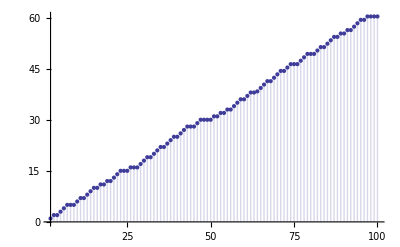

```mathematica
DiscretePlot[ GG[n,1,-1,1],{n,2,100}]
```

```mathematica
Table[ GG[n,1,0,1],{n,2,20}]
```

{1,2,2.5,3.5,4.5,5.5,5.66667,6.16667,7.16667,8.16667,8.66667,9.66667,10.6667,11.6667,11.7083,12.7083,13.2083,14.2083,14.7083}

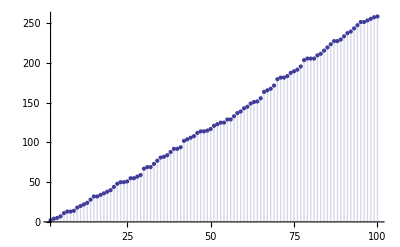

```mathematica
DiscretePlot[ GG[n,1,-1,2],{n,2,100}]
```

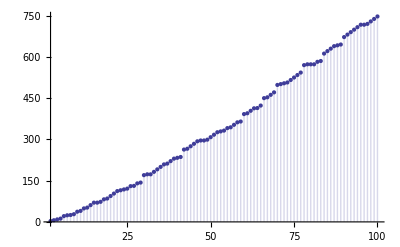

```mathematica
DiscretePlot[ GG[n,1,-1,3],{n,2,100}]
```

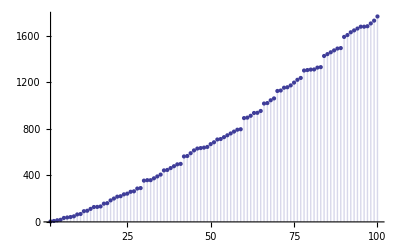

```mathematica
DiscretePlot[ GG[n,1,-1,4],{n,2,100}]
```

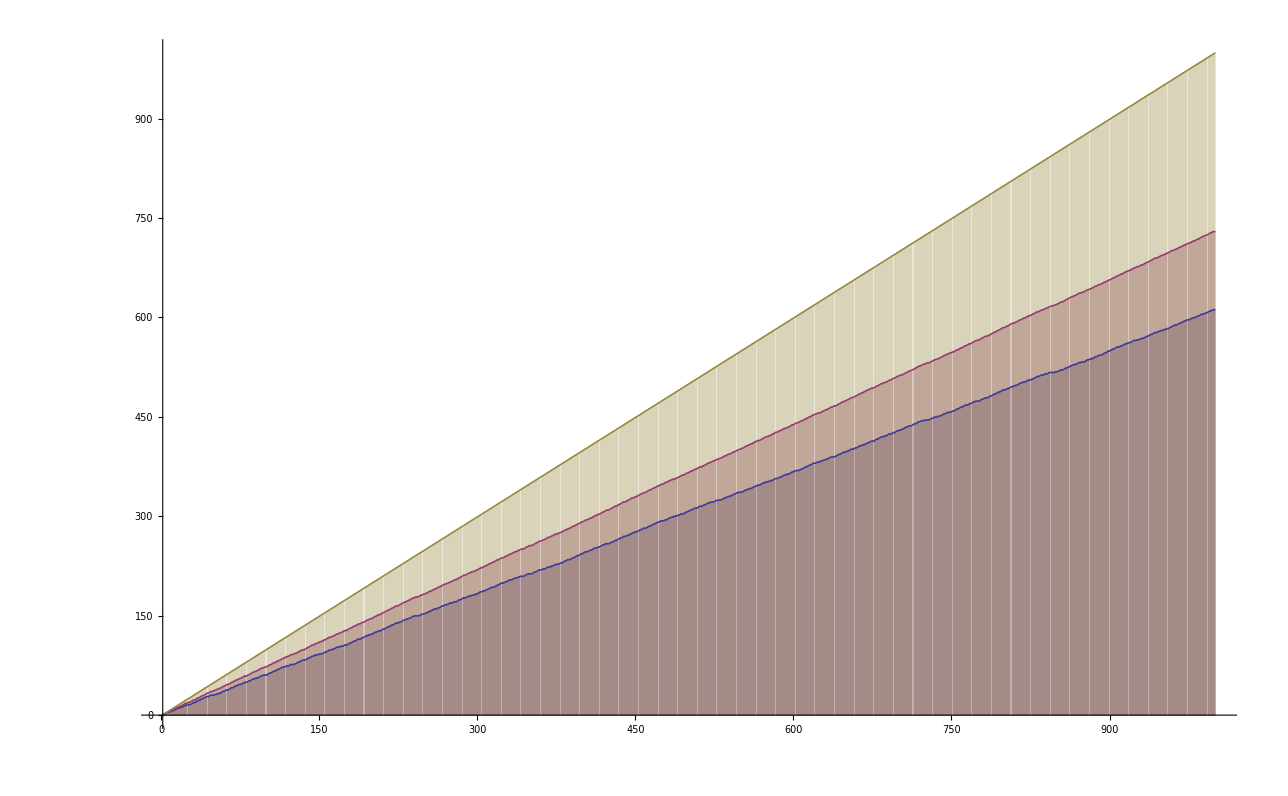

```mathematica
DiscretePlot[ {GG[n,1,-1,1], GG[n,1,0,1], GG[n,1,1,1]},{n,2,1000}, ExtentSize->Full]
```

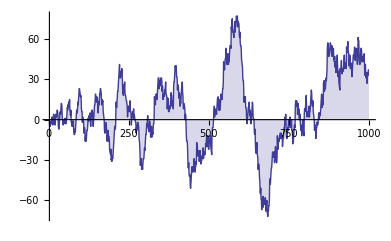

```mathematica
DiscretePlot[ GG[n,1,1,-2],{n,2,1000}]
```

```mathematica
HH[n_] := Sum[ MoebiusMu[j] Floor[ n^(1/j)]/j,{j,1,N[Log[n] + .00000001]/N[Log[2]]}]
```

```mathematica
N[HH[100]]
```

93.6

```mathematica
HHH[n_] := HH[n] - HH[n-1]
```

```mathematica
Table[HHH[n],{n,2,30}]
```

{2,1,0,1,1,1,1/3,1/2,1,1,1,1,1,1,1/2,1,1,1,1,1,1,1,1,1/2,1,2/3,1,1,1}

```mathematica
HHH[2*2*2*2*2*2*2*2*2*2*2*2]
```

1/3